#### H2+

a) write formulas for the energy levels of the bonding and anti-bonding orbitals

```mathematica
s[x_]:=Exp[-x](1+x+x^2/3)
f[x_]:=1-((1+x)Exp[-2x]-1)/x
haa[x_]:=γ^2/2-γ f[x]
hab[x_]:=-γ^2 s[x]/2-γ(2-γ)Exp[-x](1+x)
```

```mathematica
bonding[x_]:=(haa[x]+hab[x])/(1+s[x])
anti[x_]:=(haa[x]-hab[x])/(1-s[x])
```

b) For γ = 1, plot s, h_AA , and h_AB as a function of R. Explain their behavior as R → ∞, as R → 0, and
their shapes.

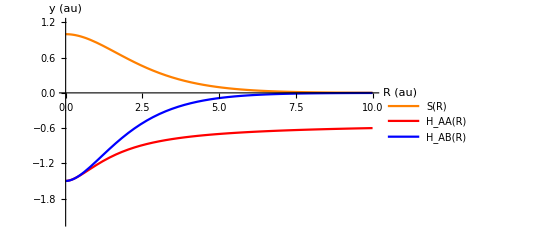

```mathematica
p1=Plot[{s[γ R]/.γ->1,haa[γ R]/.γ->1,hab[γ R]/.γ->1},{R,0,10},PlotRange->{-2.2,1.2},PlotLegends->{"S(R)","H_AA(R)","H_AB(R)"},AxesLabel->{"R (au)","y (au)"},TicksStyle->Medium,AxesStyle->Medium,PlotStyle->{{Orange,Thick},{Red,Thick},{Blue,Thick}}]
```

```mathematica
Export["h2_cation.eps",p1]
```

h2_cation.eps

```mathematica
Limit[haa[γ R]/.γ->1,R->∞]
```

-1/2

c) Repeat previous question for ϵ± (R), using your insight from those answers. Then add the
nuclear repulsion and plot both energy levels. Deduce the bond length and well-depth D e for
this approximate calculation.

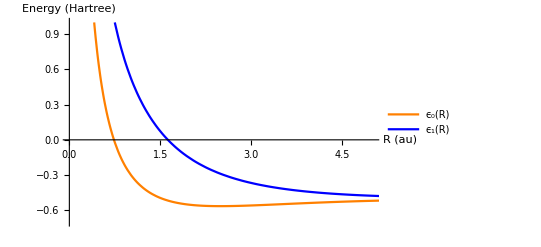

```mathematica
p2=Plot[{1/R+bonding[γ R]/.{γ->1},1/R+anti[γ R]/.{γ->1}},{R,0,10},PlotRange->{{0,5},{-0.7,1}},PlotLegends->{"ϵ_0(R)","ϵ_1(R)"},AxesLabel->{"R (au)","Energy (Hartree)"},TicksStyle->Medium,AxesStyle->Medium,PlotStyle->{{Orange,Thick},{Blue,Thick}}]
```

```mathematica
Export["h2_cat_curve.eps",p2]
```

h2_cat_curve.eps

```mathematica
D[bonding[γ R]/.γ->1+1/R,R]==0//FullSimplify
```

1/(R (7+3 ⅇ^(1+R)+R (5+R)))ⅇ^-R (9 ⅇ^(3+3 R) (-1+R)+3 ⅇ^(2+2 R) (-12+R (1+R) (7+3 R (1+R)))-3 R (1+R) (14+R (20+R (8+R)))+ⅇ^(1+R) (-35+R (-10+R (19+R (31+R (23+4 R))))))==0

```mathematica
Limit[bonding[γ R]/.γ->1,R->∞]
```

-1/2

```mathematica
Limit[bonding[γ R]/.γ->1,R->0]
```

-3/2

```mathematica
Limit[bonding[γ R]/.γ->1,R->-2]//N
```

9.66111

d) Repeat (b+c) using γ = 1 + 1/2^R , but only for the lower curve. Plot all quantities on
the same plots as before, and explain all differences. Calculate bond length and depth. Compare
with exact answers (google or NIST).

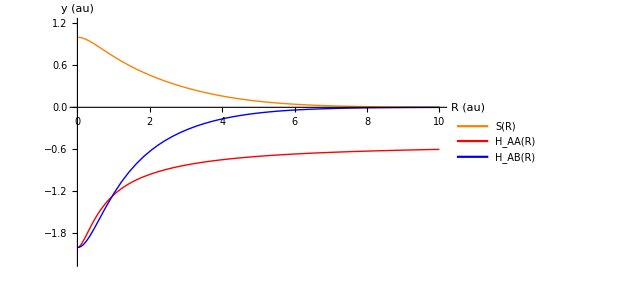

```mathematica
p3=Plot[{s[γ R]/.γ->1+1/(2^R),haa[γ R]/.γ->1+1/(2^R),hab[γ R]/.γ->1+1/(2^R)},{R,0,10},PlotRange->{-2.2,1.2},PlotLegends->Placed[{"S(R)","H_AA(R)","H_AB(R)"},{0.84,0.84}],AxesLabel->{"R (au)","y (au)"},TicksStyle->Medium,AxesStyle->Medium,PlotStyle->{{Orange,Thick},{Red,Thick},{Blue,Thick}}]
```

```mathematica
Export["h2_gamma.eps",p3]
```

h2_gamma.eps

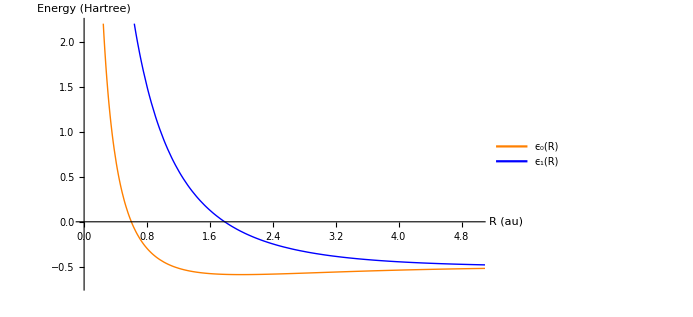

```mathematica
p4=Plot[{+1/R+bonding[γ R]/.γ->{1+1/(2^R)},1/R+anti[γ R]/.γ->1+1/(2^R)},{R,0,10},PlotRange->{{0,5},{-0.7,2.2}},PlotLegends->Placed[{"ϵ_0(R)","ϵ_1(R)","Nuclear \nRepulsion"},{0.84,0.84}],AxesLabel->{"R (au)","Energy (Hartree)"},TicksStyle->Medium,AxesStyle->Medium,PlotStyle->{{Orange,Thick},{Blue,Thick}}]
```

```mathematica
Export["h2_gamma_curve.eps",p4]
```

h2_gamma_curve.eps

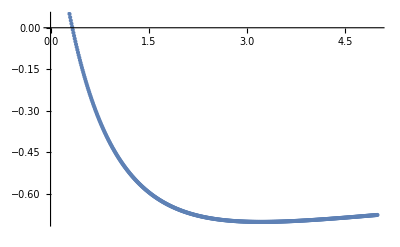

```mathematica
ListPlot[Import["gam1_bind.csv"]]
```

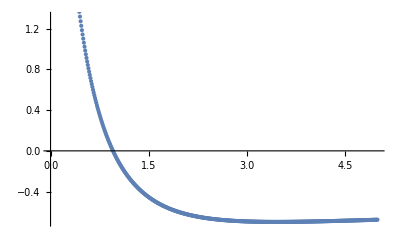

```mathematica
ListPlot[Import["gamopt_bind.csv"]]
```

#### H2

a) Plot the HF binding energy of H 2 , approximating the Hartree energy,
using the HF energy and using the same γ as in H2+.

```mathematica
hartree[x_]:=(5γ)/8(1+Exp[-x/4])
hfenergy[x_]:=2bonding[x]+hartree[x]/2
```

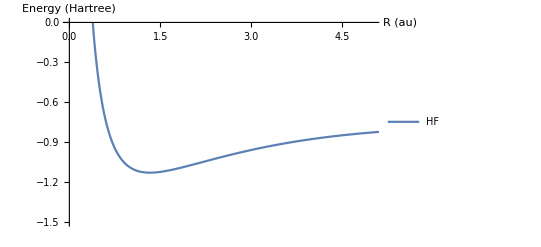

```mathematica
hfp=Plot[1/R+hfenergy[γ R]/.γ->{1+1/(2^R)},{R,0,10},PlotRange->{{0,5},{-1.5,0}},AxesLabel->{"R (au)","Energy (Hartree)"},TicksStyle->Medium,AxesStyle->Medium,PlotLegends->{"HF"}]
```

```mathematica
Export["hf_energy.eps",hfp]
```

hf_energy.eps

```mathematica
Limit[1/R+hfenergy[γ R]/.γ->{1+1/(2^R)},R->∞]//N
```

{-0.6875}

b)  Find  the  equilibrium  bond  distance  and  well-depth  from  your  curve.   Compare  with  the accurate HF values and comment.

```mathematica
D[1/R+hfenergy[γ R]/.γ->{1+1/(2^R)},{R,2}]/.R->1.18
```

{0.803522}

```mathematica
morsedata=Import["fort_60.csv","Data"]//Short
```

{{0.01,0.525272},«498»,{5,-«13»}}

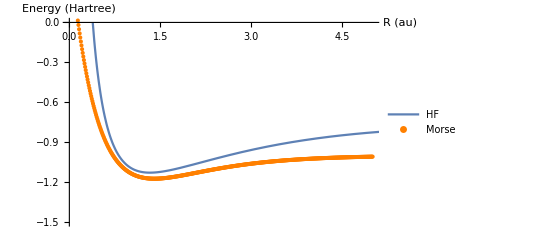

```mathematica
morse=Show[hfp,ListPlot[{Import["fort_60.csv"]},PlotStyle->Orange,PlotLegends->{"Morse"}]]
```

```mathematica
Export["hf_morse_comp.eps",morse]
```

hf_morse_comp.eps

```mathematica
h2hf=Import["H2HF.csv","Data"]//Short
```

{{0.01,97.2432},«498»,{5.,-«19»}}

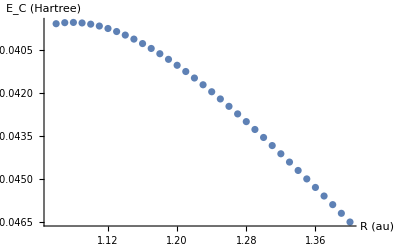

```mathematica
diff=ListPlot[Import["diff.csv"],AxesLabel->{"R (au)","E_C (Hartree)"},TicksStyle->Medium,AxesStyle->Medium]
```

```mathematica
Export["diff_hfmorse.eps",diff]
```

diff_hfmorse.eps